## Constants

```mathematica
(*everything in freq units*)
h = 6.62607015 10^-34;
ℏ = h/(2 π);
μB = 1.4 (*9.274009994 10^-24/h /10^10;*)(*h MHz*);

μI = 7.62 10^-4;
ahfP2o3 = -7.585  ; (*MHz*)
ahfS = -285.7308  ;(*MHz*)
bhfP203 = -3.445 ; (*MHz*)
nucspin = 4;
gI = 0.000176490;
gJS = 2.00229421;
ahf = -h 285.7308 10^6;
gJ = 2.00231930436256;
```

## Hhf

### J = 3/2

```mathematica
S=4; (*nuclear spin of K40*)
Ix =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iy=Table[(KroneckerDelta[m,n+1]-KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iz=-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}];
Iplus = Table[KroneckerDelta[m,n+1](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Iminus =  Table[KroneckerDelta[m+1,n](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Isq =  Table[KroneckerDelta[m,n](S*(S+1)),{m,-S,S},{n,-S,S}];
```

```mathematica
S=3/2; (*J*)
Jx =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jy=Table[(KroneckerDelta[m,n+1]-KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jz=-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}];
Jplus = Table[KroneckerDelta[m,n+1](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jminus =  Table[KroneckerDelta[m+1,n](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jsq =  Table[KroneckerDelta[m,n](S*(S+1)),{m,-S,S},{n,-S,S}];
```

```mathematica
Sumterm = ahfP2o3*(KroneckerProduct[Ix,Jx]+KroneckerProduct[Iy,Jy]+KroneckerProduct[Iz,Jz]);
```

```mathematica
term2 = μB gJS KroneckerProduct[IdentityMatrix[9],Jz]+μI*gI*KroneckerProduct[Iz,IdentityMatrix[4]];
```

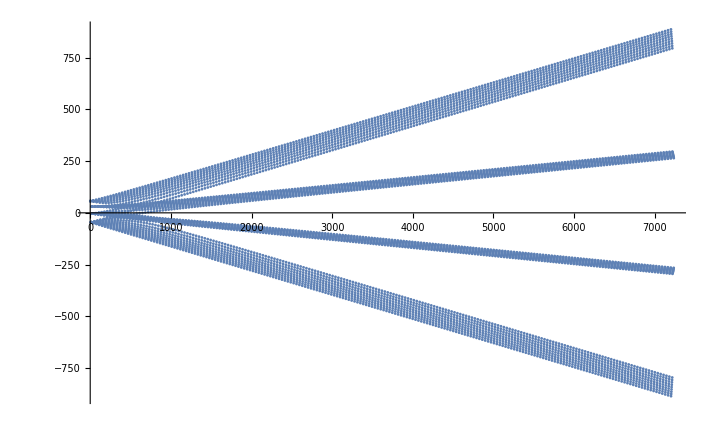

```mathematica
table2 = Table[Eigenvalues[Sumterm+ term2 B],{B,0,200}];

ListPlot@Flatten[table2]
(*axes {"B Field (G)","E (h MHz)"}*)
```

### J = 1/2

```mathematica
S=1/2;
Jx2 =Table[(KroneckerDelta[m,n+1]+KroneckerDelta[m+1,n])*1/2*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jy2=Table[(KroneckerDelta[m,n+1]-KroneckerDelta[m+1,n])*1/(2*I)*(S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jz2=-Table[(KroneckerDelta[m,n])*n,{m,-S,S},{n,-S,S}];
Jplus = Table[KroneckerDelta[m,n+1](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jminus =  Table[KroneckerDelta[m+1,n](S*(S+1)-m*n)^(1/2),{m,-S,S},{n,-S,S}];
Jsq =  Table[KroneckerDelta[m,n](S*(S+1)),{m,-S,S},{n,-S,S}];
```

```mathematica
Sumterm3 = ahfS (KroneckerProduct[Ix,Jx2]+KroneckerProduct[Iy,Jy2]+KroneckerProduct[Iz,Jz2]);
```

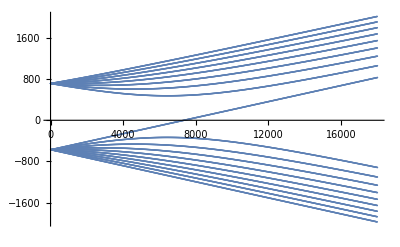

```mathematica
term3 = μB gJS KroneckerProduct[IdentityMatrix[9],Jz2]+μI*gI*KroneckerProduct[Iz,IdentityMatrix[2]];
table = Table[Eigenvalues[Sumterm3+ term3 B],{B,0,1000}];

ListPlot@Flatten[table]
```

## Breit-Rabi

```mathematica
Ehf[mF_,B_]:= -ahfS/4+gI μB mF B + (ahfS(nucspin+1/2))/2(1 + (4 mF ((gJS μB - gI μB)/(ahfS (nucspin+1/2))B))/(2nucspin + 1)+((gJS μB - gI μB)/(ahfS (nucspin+1/2))B)^2)^(1/2)
```

```mathematica
Ehf9o2[mF_,B_]:= -ahfS/4+gI μB mF B + (ahfS(nucspin+1/2))/2(1 + ((gJS μB - gI μB)/(ahfS (nucspin+1/2))B))
```

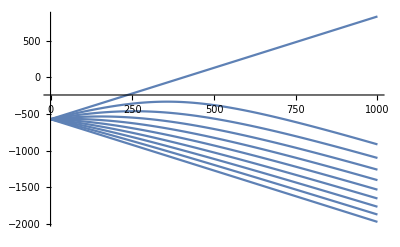

```mathematica
p1 = Plot[Ehf[Range[-9/2,7/2],B],{B,0,1000},PlotRange->All,FrameLabel->{"B (G)","Ehf/h (MHz)"}];
p2 = Plot[Ehf9o2[9/2,B],{B,0,1000},PlotRange->All,FrameLabel->{"B (G)","Ehf/h (MHz)"}];
Show[{p1,p2}]
```

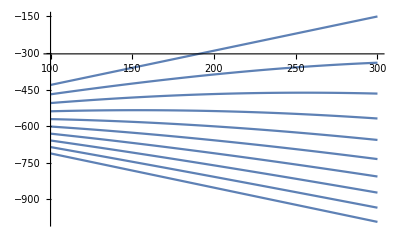

```mathematica
p1 = Plot[Ehf[Range[-9/2,7/2],B],{B,100,300},PlotRange->All];
p2 = Plot[Ehf9o2[9/2,B],{B,100,300},PlotRange->All];
Show[{p1,p2},FrameLabel->{"B (G)","Ehf/h (MHz)"}]
```

```mathematica
Ehf[-9/2,202.1]
```

-854.926

## B to freq

```mathematica
ωhf[in__]:=Ehf[in]
FreqMHz[B_,mF_,mF2_]:=  ωhf[B,mF]-ωhf[B,mF2];
```

```mathematica
FreqMHz[199.5,-7/2,-9/2]
```

46.7348

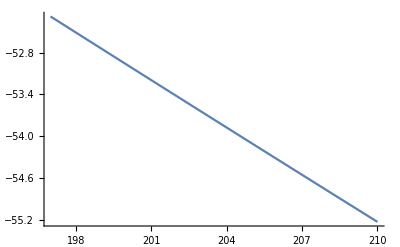

```mathematica
Plot[FreqMHz[B,-5/2,-3/2],{B,197,210}]
```

```mathematica
(*from labs code*)
```

```mathematica
EhfF[B_,F_,mF_] := - ahf/4+gI μB mF B +(-1)^(F-1/2) (ahf 9/2)/2 √(1+ (4mF)/(2 9/2)( ((gJ-gI)μB)/(ahf 9/2)B)+( ((gJ-gI)μB)/(ahf 9/2)B)^2);
ωhfF[in__]:=EhfF[in]
FreqMHz[B_,F1_,mF1_,F2_,mF2_]:=ωhfF[B,F1,mF1]-ωhfF[B,F2,mF2];
```

```mathematica
FreqMHz[199.5,9/2,-7/2,9/2,-9/2]
```

0.0492937

```mathematica
EhfF[202.1,9/2,-7/2]
```

-283.418